```mathematica
propPlot[country_,property_]:=Module[{Question1,dataQuestion1,cleanedDataQ1,valuesQ1,averagevalues,maximumvalues,minimumvalues,maximumpoint,minimumpoint,xAXISminimum,xAXISmaximum},
Question1=CountryData[country,{property,All}];
dataQuestion1=Normal[Question1["Path"]];
cleanedDataQ1=Map[{DateValue[#[[1]],"Year"],QuantityMagnitude[#[[2]]]}&,dataQuestion1];
cleanedDataQ1=Select[cleanedDataQ1,NumberQ[Last[#]]&&1960<=First[#]<=2022&];
valuesQ1=cleanedDataQ1[[All,2]];
averagevalues=Mean[valuesQ1];
maximumvalues=Max[valuesQ1];
minimumvalues=Min[valuesQ1];
maximumpoint=SortBy[cleanedDataQ1,Last][[-1]];
minimumpoint=SortBy[cleanedDataQ1,Last][[1]];
xAXISminimum=Min[cleanedDataQ1[[All,1]]];
xAXISmaximum=Max[cleanedDataQ1[[All,1]]];

plotLines={{Thick,Dashed,InfiniteLine[{0,averagevalues},{1,0}]},{Thin,Dashed,InfiniteLine[{0,maximumvalues},{1,0}]},{Thin,Dashed,InfiniteLine[{0,minimumvalues},{1,0}]},{Black,PointSize[Large],Point[{maximumpoint,minimumpoint}]}};

ListLinePlot[cleanedDataQ1,PlotLabel->property<>" for "<>country<>" over the years",AxesLabel->{"year",property},Epilog->{{Thick,Dashed,Line[{{xAXISminimum,averagevalues},{xAXISmaximum,averagevalues}}]},{Thin,Dashed,Line[{{xAXISminimum,maximumvalues},{xAXISmaximum,maximumvalues}}]},{Thin,Dashed,Line[{{xAXISminimum,minimumvalues},{xAXISmaximum,minimumvalues}}]},{Black,PointSize[Large],Point[maximumpoint]},{Black,PointSize[Large],Point[minimumpoint]}}]]

(*Testing Functions*)
propPlot["Brazil","GDPPerCapita"]
propPlot["Pakistan","GDPPerCapita"]
```

```mathematica
dataQuestion2=Select[{CountryData[#,"Name"],QuantityMagnitude[CountryData[#,"GDPPerCapita"]],QuantityMagnitude[CountryData[#,"LiteracyFraction"]]}&/@CountryData[],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];
maximumvalue=60000;

Question2=DynamicModule[{gdpThreshold=10000},Column[{Slider[Dynamic[gdpThreshold],{0,maximumvalue}],Dynamic[ListPlot[{Tooltip[{#[[3]],#[[2]]},#[[1]]]&/@Select[dataQuestion2,#[[2]]<=gdpThreshold&],Tooltip[{#[[3]],#[[2]]},#[[1]]]&/@Select[dataQuestion2,#[[2]]>gdpThreshold&]},PlotStyle->{Pink,Green},PlotLegends->{"GDP % less than $"<>ToString[Round[gdpThreshold]],"GDP % greater than $"<>ToString[Round[gdpThreshold]]},AxesLabel->{"literacy","wealth"}]]}]]
```

```mathematica
dataQuestion2=Select[{CountryData[#,"Name"],QuantityMagnitude[CountryData[#,"GDPPerCapita"]],QuantityMagnitude[CountryData[#,"LiteracyFraction"]]}&/@CountryData[],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];

maximumvalue=60000;

dataQuestion2=Select[{CountryData[#,"Name"],QuantityMagnitude[CountryData[#,"GDPPerCapita"]],QuantityMagnitude[CountryData[#,"LiteracyFraction"]]}&/@CountryData[],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];

maximumvalue=60000;
scaleFactor=1000000;

Question2=dataQuestion2=Select[Table[{CountryData[c,"Name"],QuantityMagnitude[CountryData[c,"GDPPerCapita"]],QuantityMagnitude[CountryData[c,"LiteracyFraction"]]},{c,CountryData[]}],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];

maximumvalue=60000;
scaleFactor=1000000;

Question2=Manipulate[Module[{belowData,aboveData},belowData=Select[dataQuestion2,#[[2]]<=threshold&];
aboveData=Select[dataQuestion2,#[[2]]>threshold&];
ListPlot[{If[Length[belowData]>0,Table[Tooltip[{row[[3]],row[[2]]/scaleFactor},row[[1]]],{row,belowData}],{}],If[Length[aboveData]>0,Table[Tooltip[{row[[3]],row[[2]]/scaleFactor},row[[1]]],{row,aboveData}],{}]},PlotStyle->{Blue,Orange},PlotLegends->{"GDP pc less than $"<>ToString[Round[threshold]],"GDP pc greater than $"<>ToString[Round[threshold]]},AxesLabel->{"literacy","wealth"},Ticks->{Automatic,{0,0.02,0.04,0.06,0.08,0.10}}]],{{threshold,10000,"gdpThreshold"},0,maximumvalue}]
```

```mathematica
dataQuestion2=Select[Table[{CountryData[c,"Name"],QuantityMagnitude[CountryData[c,"GDPPerCapita"]],QuantityMagnitude[CountryData[c,"LiteracyFraction"]]},{c,CountryData[]}],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];

maximumvalue=60000;
scaleFactor=1000000;

Question2=Manipulate[Module[{belowData,aboveData,plotData,plotColors,legendLabels},belowData=Select[dataQuestion2,#[[2]]<=threshold&];
aboveData=Select[dataQuestion2,#[[2]]>threshold&];
plotData={};
plotColors={};
legendLabels={};
If[Length[belowData]>0,AppendTo[plotData,Table[Tooltip[{row[[3]],row[[2]]/scaleFactor},row[[1]]],{row,belowData}]];
AppendTo[plotColors,Blue];
AppendTo[legendLabels,"GDP pc less than $"<>ToString[Round[threshold]]]];
If[Length[aboveData]>0,AppendTo[plotData,Table[Tooltip[{row[[3]],row[[2]]/scaleFactor},row[[1]]],{row,aboveData}]];
AppendTo[plotColors,Orange];
AppendTo[legendLabels,"GDP pc greater than $"<>ToString[Round[threshold]]]];
ListPlot[plotData,PlotStyle->plotColors,PlotLegends->legendLabels,AxesLabel->{"literacy","wealth"},Ticks->{Automatic,{0,0.02,0.04,0.06,0.08,0.10}}]],{{threshold,10000,"gdpThreshold"},0,maximumvalue}]
```

```mathematica
dataQuestion2=Select[Table[{CountryData[c,"Name"],QuantityMagnitude[CountryData[c,"GDPPerCapita"]],QuantityMagnitude[CountryData[c,"LiteracyFraction"]]},{c,CountryData[]}],NumericQ[#[[2]]]&&NumericQ[#[[3]]]&];

maximumvalue=60000;

Question2=Manipulate[Module[{belowData,aboveData,plotData,plotColors,legendLabels},belowData=Select[dataQuestion2,#[[2]]<=threshold&];
aboveData=Select[dataQuestion2,#[[2]]>threshold&];
plotData={};
plotColors={};
legendLabels={};

If[Length[belowData]>0,AppendTo[plotData,Table[Tooltip[{row[[3]],row[[2]]},row[[1]]],{row,belowData}]];
AppendTo[plotColors,Blue];
AppendTo[legendLabels,"GDP % less than $"<>ToString[Round[threshold]]]];

If[Length[aboveData]>0,AppendTo[plotData,Table[Tooltip[{row[[3]],row[[2]]},row[[1]]],{row,aboveData}]];
AppendTo[plotColors,Orange];
AppendTo[legendLabels,"GDP % greater than $"<>ToString[Round[threshold]]]];
ListPlot[plotData,PlotStyle->plotColors,PlotLegends->legendLabels,AxesLabel->{"literacy","wealth"},PlotRange->{Automatic,{0,All}}]],{{threshold,10000,"gdpThreshold"},0,maximumvalue}]
```

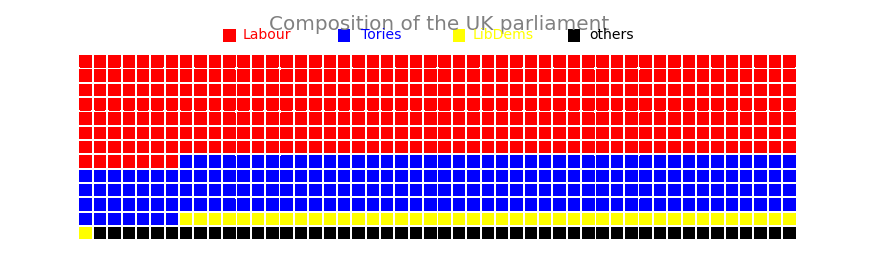

```mathematica
parliament[labour_,tories_,libdems_]:=Module[{others,allseats,seatcolors,squares,title,legend},others=650-labour-tories-libdems;
allseats=Join[Table[Red,labour],Table[Blue,tories],Table[Yellow,libdems],Table[Black,others]];
seatcolors=Partition[allseats,50];
squares=Table[{seatcolors[[row,col]],Rectangle[{col-1,13-row},{col-0.2,13-row+0.8}]},{row,1,13},{col,1,50}];
title=Text[Style["Composition of the UK parliament",20,Gray],{25,15}];
legend={{Red,Rectangle[{10,13.8},{10.8,14.6}]},Text[Style["Labour",14,Red],{13,14.2}],{Blue,Rectangle[{18,13.8},{18.8,14.6}]},Text[Style["Tories",14,Blue],{21,14.2}],{Yellow,Rectangle[{26,13.8},{26.8,14.6}]},Text[Style["LibDems",14,Yellow],{29.5,14.2}],{Black,Rectangle[{34,13.8},{34.8,14.6}]},Text[Style["others",14,Black],{37,14.2}]};
Graphics[{squares,title,legend},ImageSize->800]]

parliament[357,200,44]
```

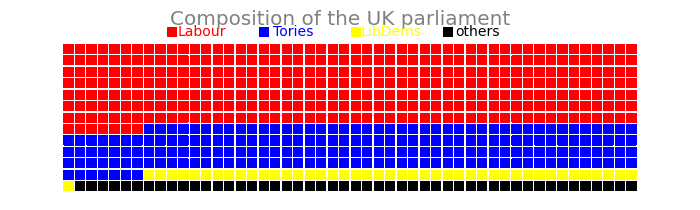

```mathematica
parliament[labourseats_,toryseats_,libdemseats_]:=Module[{otherseats,allseatsquestion3,gridquestion3,squaresquestion3,titlequestion3,legendquestion3},

otherseats=650-labourseats-toryseats-libdemseats;

allseatsquestion3=Flatten[{Table[Red,labourseats],Table[Blue,toryseats],Table[Yellow,libdemseats],Table[Black,otherseats]}];
gridquestion3=Partition[allseatsquestion3,50];

squaresquestion3=Table[{gridquestion3[[row,col]],Rectangle[{col,14-row},{col+0.8,14-row+0.8}]},{row,13},{col,50}];

titlequestion3=Text[Style["Composition of the UK parliament",20,Gray],{25,16}];

legendquestion3={Red,Rectangle[{10,14.5},{10.8,15.3}],Text[Style["Labour",14,Red],{13,14.9}],Blue,Rectangle[{18,14.5},{18.8,15.3}],Text[Style["Tories",14,Blue],{21,14.9}],Yellow,Rectangle[{26,14.5},{26.8,15.3}],Text[Style["LibDems",14,Yellow],{29.5,14.9}],Black,Rectangle[{34,14.5},{34.8,15.3}],Text[Style["others",14,Black],{37,14.9}]};

Graphics[{squaresquestion3,titlequestion3,legendquestion3},ImageSize->700]]

parliament[357,200,44]
```